```mathematica
TakeIndex[x_,y_,data_]:=Transpose[{Transpose[data][[x]],Transpose[data][[y]]}]
```

1: Actuator ID
2 : Time
3:raw pos
4: pos estimate
5:goal pos
6: error
7: set speed
8: at valid angle
9: average speed

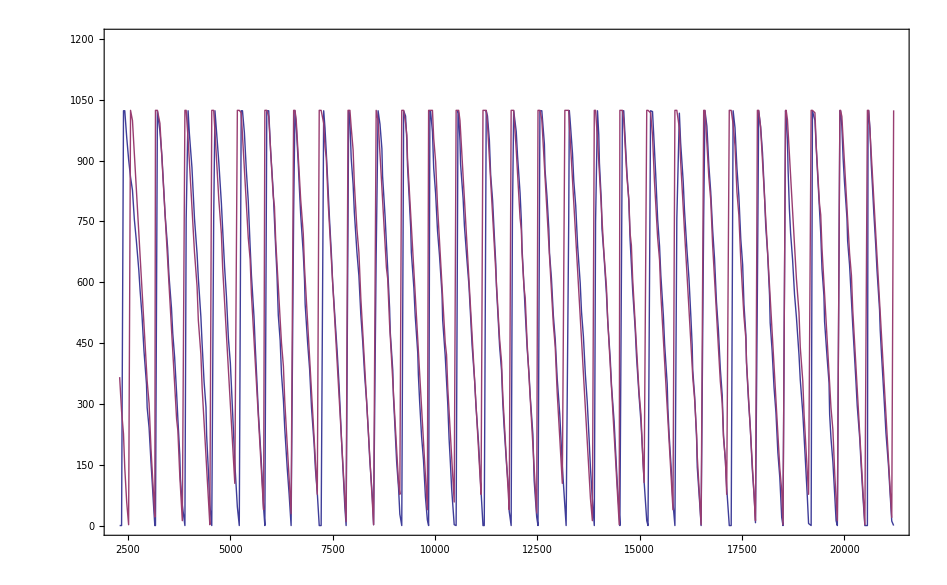

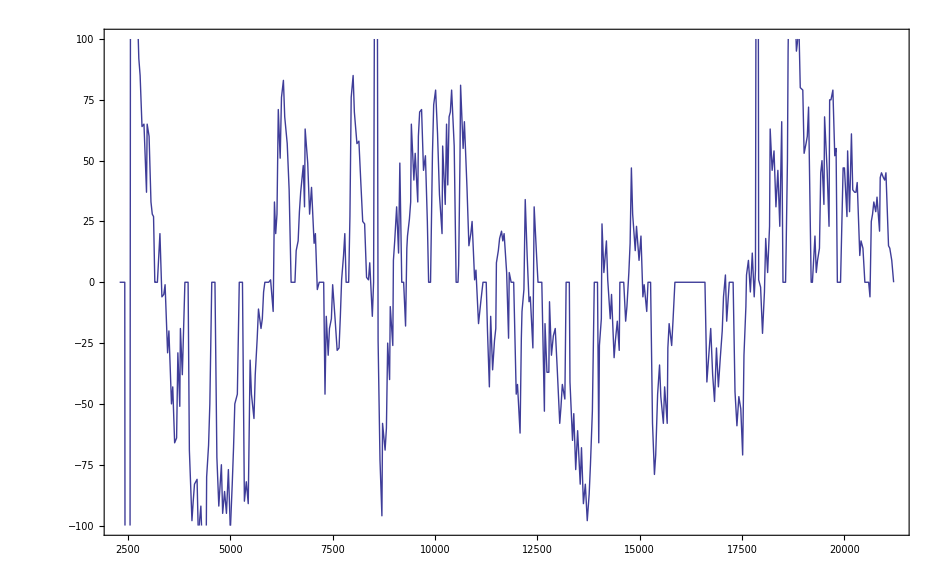

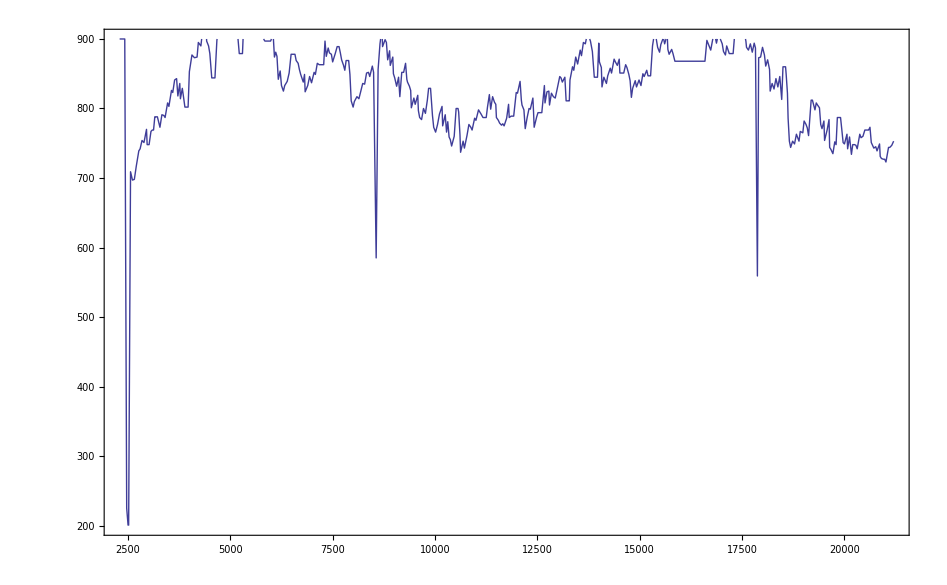

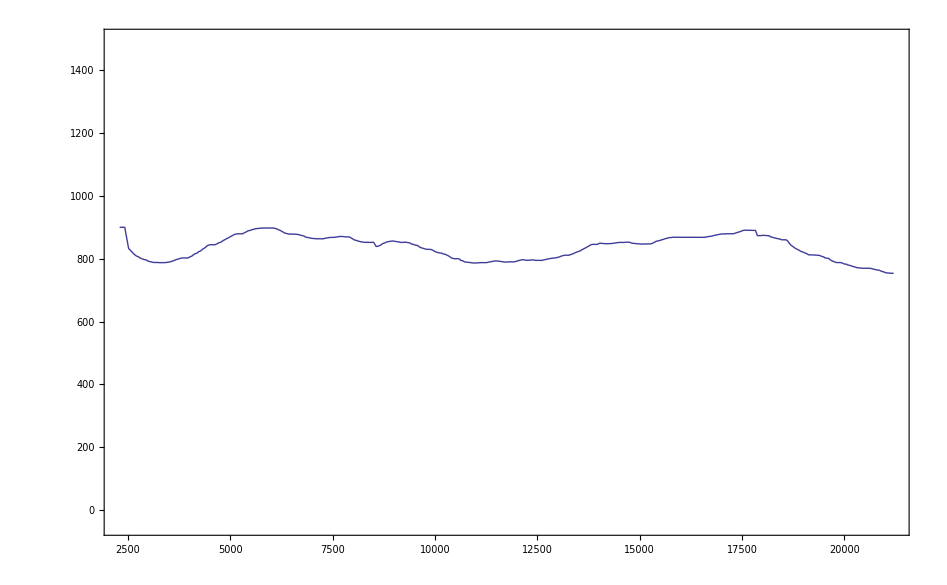

```mathematica
data=Import[NotebookDirectory[]<>"..\..\d2u\pos.log","Table"];
data0=Select[data,#[[1]]==0&];
data1=Select[data,#[[1]]==1&];
ListPlot[{TakeIndex[2,3,data0],TakeIndex[2,5,data0]},PlotJoined->True, PlotRange->{0,1200},Frame->True]
ListPlot[{TakeIndex[2,6,data0]},PlotJoined->True, PlotRange->{-100,100},Frame->True]
ListPlot[{TakeIndex[2,7,data0]},PlotJoined->True, PlotRange->{200,900},Frame->True]
ListPlot[{TakeIndex[2,9,data0]},PlotJoined->True, PlotRange->{-50-0,1500},Frame->True]
```

```mathematica
700/1.25
```

560.

```mathematica
600.*0.25
```

150.

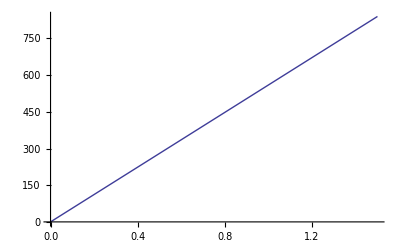

```mathematica
Plot[560.*x,{x,0,1.5}]
```

```mathematica
1000000/57142.
```

17.5003